```mathematica
An[x_]:= x(1-x) * Sin[((Pi * (2n-1))/2) *x]
```

```mathematica
Integrate[An[x], x]
```

(2 (-8+(1-2 n)^2 π^2 (-1+x) x) Cos[1/2 (-1+2 n) π x]-4 (-1+2 n) π (-1+2 x) Sin[1/2 (-1+2 n) π x])/((-1+2 n)^3 π^3)

```mathematica
Integrate[An[x], {x, 0, 1}]
```

```mathematica
(4 (4+(-1+2 n) π Cos[n π]-4 Sin[n π]))/((-1+2 n)^3 π^3)
testAn = (4 (4+(-1+2 n) π Cos[n π]-4 Sin[n π]))/((-1+2 n)^3 π^3)
```

(4 (4+(-1+2 n) π Cos[n π]-4 Sin[n π]))/((-1+2 n)^3 π^3)

```mathematica
(4 (4+(-1+2 n) π Cos[n π]-4 Sin[n π]))/((-1+2 n)^3 π^3)
myAn = 2 *(Pi * (2n-1) * 4 * (-1)^n + 16) / ( (Pi^3) * ((2n - 1)^3))
```

(4 (4+(-1+2 n) π Cos[n π]-4 Sin[n π]))/((-1+2 n)^3 π^3)

(2 (16+4 (-1)^n (-1+2 n) π))/((-1+2 n)^3 π^3)

```mathematica
F[x_,m_]:= Sum[myAn* Sin[((Pi * (2*n-1))/2) * x], {n, 1, m}]
```

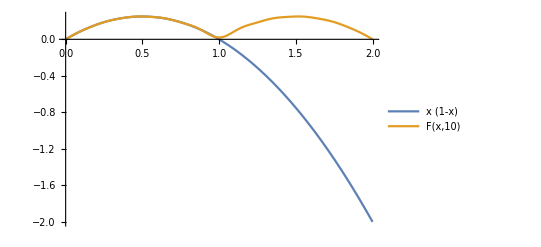

```mathematica
Plot[{x*(1-x),F[x, 10]}, {x, 0, 2}, PlotLegends->"Expressions"]
```

```mathematica
Lam = - (Pi * (2n-1))^2;
F2[x_, t_, m_]:= Sum[Exp[Lam * t]*myAn* Sin[((Pi * (2*n-1))/2) * x], {n, 1, m}]
Plot3D[F2[x, t, 10], {x, 0, 1}, {t, 0, .1}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
An2 = (2/ (Pi *n) ) * Sin[ (n * Pi) / 2]
```

(2 Sin[(n π)/2])/(n π)

```mathematica
G[x_,m_]:=.5 +  Sum[An2* Cos[n * x], {n, 1, m}]
```

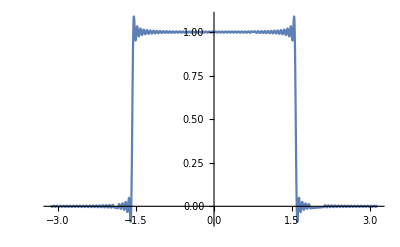

```mathematica
Plot[G[x, 100], {x, -Pi, Pi}]
```

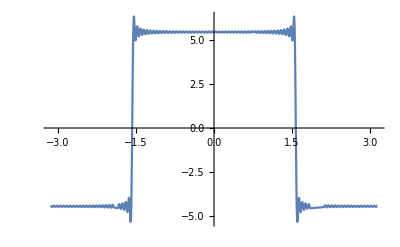
```mathematica
-Graphics-

Plot[Cos[x], {x, -Pi/2, Pi/2}]
```

-Graphics-